# Generate Plots

To the point, just the facts, ma’am, leave all the trial and error to the main, long notebook GWExopEcc2.nb.

## Strain calculations for exoplanets in the Caltech database. Calculate with eccentricity and distance, etc, the strain at Earth. Frequencies relevant for LISA.

## Notes

20171013 Started taking best bits from GWExopEcc2.nb, and trying to generate the publication quality plots here and not in XMGrace with *.dat files.

## References

P. Amaro-Seoane et al. “Triplets of supermassive black holes: astrophysics, gravitational waves and detection,” MNRAS 402 2308-2320 (2010);
P. C. Peters and J. Mathews, “Gravitational Radiation from Point Masses in a Keplerian Orbit,” Phys. Rev. 131 (1963) 435-440.
Michele Maggiore, “Gravitational Waves. Volume 1: Theory and Experiments,” Oxford Univ. Press, 2008.

## Directories

```mathematica
(*myDir = "/scratch/gabella/Documents/astro/exop/";*)
(*thisDir = "/home/gabella/Documents/astro/exop/exoplanetsMath/";*)
thisDir = NotebookDirectory[];
csvDir = thisDir <>"dbases/";
pixDir = thisDir <>"pix/";
```

## Read the CSV file, filter data for non-null entries.

### Run ExoDBase.nb to re-create the cvs file.

```mathematica
csvFileName = csvDir<>"exop_20171011_144256.csv"
```

/home/gabella/Documents/astro/exop/exoplanetsMath/dbases/exop_20171011_144256.csv

Find the date-time stamp...lots of StringSplit[]’s.  Will be used in output file names.

```mathematica
dateTimeStamp = Block[{aa,bb,cc},
aa = StringSplit[csvFileName,"/"][[-1]];  (* Filename with stamp is last element. *)
bb = StringSplit[aa,"."][[1]]; (* Drop the .csv extension . *)
cc = StringSplit[bb, "_"]; (* Last two elements are the YYYYMMDD and the HHMMSS strings. *) 
cc[[2]]<>"_"<>cc[[3]]
]
```

20171011_144256

Has first row has the columns and other info.  Mathematica lets the data be mixed format, some are strings others reals.

```mathematica
alldata = Import[csvFileName, "Data"];
```

```mathematica
alldata[[1;;3]] //TableForm(* Look for the row headers. *)
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92

```mathematica
rowHeaders=1; rowDataStart=rowHeaders+1;  (* row with the headers, etc . *)
```

Cols are 
rowid, pl_hostname, pl_letter, pl_orbper, pl_orbsmax, pl_orbeccen, pl_bmassj, st_dist, st_mass, pl_name, pl_massj
# COLUMN pl_hostname:    Host Name
# COLUMN pl_letter:      Planet Letter
# COLUMN pl_orbper:      Orbital Period [days]
# COLUMN pl_orbsmax:     Orbit Semi-Major Axis [AU]
# COLUMN pl_orbeccen:    Eccentricity
# COLUMN pl_bmassj:      Planet Mass or M*sin(i)[Jupiter mass]
# COLUMN st_dist:        Distance [pc]
# COLUMN st_mass:        Stellar Mass [Solar mass]
# COLUMN pl_name:        Planet Name
# COLUMN pl_massj:       Planet Mass [Jupiter mass]
# COLUMN st_plx:	Star parallax distance [mas], NB: dist in pc is 1000.0/st_plx (in mas)

Find the type of the data fields, when they are actually numbers and not blanks!  Mix of Strings and Reals.

```mathematica
Print["Length of the column, the number of columns is ", Length[ alldata[[rowDataStart]] ]  ]
```

Length of the column, the number of columns is 11

Make a dictionary, aka Association in Mathematica, with the header strings to the column numbers / array indices.

```mathematica
cols = <||>;  (* Use an Association as an enum, or Dictionary *)
For[icnt=1, icnt≤Length[ alldata[[rowHeaders]] ], icnt+=1,
AppendTo[cols,alldata[[rowHeaders,icnt]]->icnt]
];
```

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
{cols["pl_hostname"], cols["pl_orbper"]}
```

{1,4}

#### Filter data for the non-null data only.

Some of the fields are blank, so drop those planets from consideration.  Define a filter function.

```mathematica
Clear[filterBlanks2]
filterBlanks2[aa_, filterInd_]:=Module[{retList, blankList},
retList={};
blankList={};
For[i=1,i<=Length[aa], i++,
If[ NumberQ[ aa[[i,filterInd]] ], AppendTo[retList, aa[[i]] ], AppendTo[blankList, aa[[i]] ]]
];
{retList, blankList}
]
```

Filter the blanks in all masses, eccentricity, semimajor axis, and distance.

```mathematica
Print["Length alldata ",Length[alldata] ]
tempdata = alldata;
tempdata= filterBlanks2[tempdata[[rowDataStart;;]], cols["pl_orbeccen"] ][[1]]; Print[ "Number with pl_orbeccen ", Length[tempdata]]
tempdata= filterBlanks2[tempdata, cols["pl_orbper"] ][[1]]; Print[ "Number with pl_orbper ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["pl_orbsmax"] ][[1]]; Print["Number with pl_orbsmax ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["pl_bmassj"] ][[1]]; Print["Number with pl_bmassj ",Length[tempdata] ] (* use pl_bmassj not pl_massj *)
tempdata = filterBlanks2[tempdata, cols["st_dist"] ][[1]]; Print["Number with st_dist ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["st_mass"] ][[1]]; Print["Number with st_mass ",Length[tempdata] ]
```

Length alldata 3530

Number with pl_orbeccen 1112

Number with pl_orbper 1112

Number with pl_orbsmax 1049

Number with pl_bmassj 989

Number with st_dist 889

Number with st_mass 858

The filtered data, and it should have same length as last step above.

```mathematica
fdata = tempdata; (* The filtered data. *)
Length[fdata]
```

858

## Eccentric orbits from the exoplanet database.

### Some constants. Work in SI units. Okay, join the astro / GR world and look at units of length for mass, etc, that is G=c=1 type of unit conversion.

```mathematica
massSun = 1.99 10^30; (*kg *)
massJ = 1.9 10^27; (* kg *)
massE = 5.97 10^24; (* kg *)
massJe = massJ/massE; (* Jupiter mass is 317.9 earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
secsYear = 365.24*24.0*3600.0; (* s, number of seconds in a year *)
secsDay = 24.0*3600.0; (* s, number of seconds in a day *)
bigG = 6.67384 10^-11; (* SI Gravitational constant, m^3/kg/s *)

rscon = 2*bigG*massSun/cee^2 (* 2955.43 m, solar mass Scharzschild radius *)
lunits =bigG*massSun/cee^2 (* meters per solar mass, units of G=c=1, no factor of 2 as in Schwarzschild radius *)
masscon = lunits; (* m, G Msol/c^2, for 1 solar mass *)

powercon = cee^5/bigG  (* 3.628 10^52 W, c^5/G, W/unit since P is dimensionless in G=c=1 units *)
energycon = cee^4/bigG  (* 1.210 10^44 J/m, c^4/G *)
```

2955.41

1477.7

3.6285×10^52

1.21034×10^44

### The functions of interest.

Removed three plus g(n,e)  here ggXX[] comparison section to file ThreeGsGWEccen.nb .

Amaro-Seoane et al.

```mathematica
Clear[bigAAS, bigBAS, jj]
jj = BesselJ
bigAAS[n_,e_]:=jj[n-2,n e]-2 jj[n, n e]+jj[n+2,n e]
bigBAS[n_,e_]:=jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n,n e]+2 e jj[n+1,n e]-jj[n+2,n e]
ggAS[n_, e_]:=n^4/32(bigBAS[n,e]^2 + (1-e^2)bigAAS[n,e]^2+4/(3 n^2)jj[n,n e]^2)
```

BesselJ

Amaro-Seoane et al., h_n Eqn. (9).

```mathematica
Clear[chirpM,redM, totM, fr, hh]
chirpM[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5)
redM[m1_,m2_]:=(m1 m2)/(m1+m2)
totM[m1_,m2_]:=m1+m2
fr[m1_,m2_,a_]:=1/(2 π)√((bigG(m1+m2))/a^3)
hh [n_,e_,m1_,m2_,a_, dL_]:= bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/(n dL)(2π fr[m1,m2,a])^(2/3) √ggAS[n,e]  (* Subscript[d, L] is luminosity distance d=Subscript[d, L]/(1+z), z=0 for us, Subscript[f, r] is orbital freq *)
```

The numerical fit from GWExopEcc2.nb .

```mathematica
Clear[fitEcc2N2]
fitEcc2N2=FittedModel[ⅇ^(9.521217921844688 x) (0.5899926687166828-1.4130060483325517 x+0.8921018741263468 x^2)]
```

FittedModel[ⅇ^(9.52122 x) (0.589993-1.41301 x+0.892102 x^2)]

```mathematica
fitEcc2N2[0.7]
```

29.8196

Find the mode number n_max where g(n,e) falls to 0.05.  Also n_min, usually either 1 or 2.

```mathematica
Clear[aNmax];
aNmax[ecc_]:=If[ecc==0, 2, Floor[fitEcc2N2[ecc]+1]]
Clear[aNmin];
aNmin[ecc_]:=If[ecc==0,1, 1](* A little silly, but played with n=2 for e=0 since the only one but want a range, so 1 to 2 for e=0. *)
```

#### Amaro-Seoane et al. enhancement

Now for the hf calculation following Amaro-Seoane et al.  Already have h with correct units (unitless) above.  Note the G^(5/3)/c^4~6.3×10^-55.  But for strain sensitivity (??), do the AS eqn. (10) enhancement,
 hobs,n = h_n  √(T f_(r n))   , where T is max(T_orb, T_obs), 
 so that T f_(f n)= 1 or N_orbs, the latter if observed for many orbital periods.  So their formula is like a sqrt(N) incoherent addition for the noise and for thre signal it should add like N.  A lot like pulsar analysis.
Used 3 years and 10 years for LISA observing T_obs...in previous exoplanet work (Hot Jupiters).  I think almost all T_orb are less than that.

```mathematica
rootNfcn := Sqrt[ Max[ #1, #2]*#3/#1 ]&; (* #1 is Subscript[t, orb], #2 is Subscript[t, obs], same units!, #3 is the n of the GW harmonic *)
```

## The strain versus frequency of the n-th GW mode.

Leave out a lot of the “cleverness” in the handling of the column names, etc.  “Just the facts, ma’am.”

```mathematica
Length[fdata]
```

858

For each row in the data list, calculate the mode frequencies, and use the listed parameters to come up with the dimensionless strength h(n), for each mode.  imode Amaro-Seoane adjustment yet.

```mathematica
{alldata[[1]]}~Join~fdata[[1;;2]]//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92

Use the association/dictionary cols to get the right columns using the above text.

```mathematica
{cols["pl_orbper"],cols["pl_bmassj"], cols["st_dist"]}
```

{4,7,8}

All calculations in SI units, see constants above.

```mathematica
{Length[fdata], Length[fdata[[1]] ]}
```

{858,11}

```mathematica
fdata[[ipl]]/.{ ipl->1}
```

Part::pkspec1: The expression ipl cannot be used as a part specification.

{HD 142022 A,b,Radial Velocity,1928.,3.03,0.53,5.1,35.87,0.99,2014-05-14,27.88}

```mathematica
fdata[[ipl]][[cols["pl_orbeccen"] ]]/.{ ipl->1}
```

Part::pkspec1: The expression ipl cannot be used as a part specification.

Part::partw: Part 6 of {{HD 142022 A,b,Radial Velocity,1928.,3.03,0.53,5.1,35.87,0.99,2014-05-14,27.88},{HD 39091,b,Radial Velocity,2151.,3.38,0.6405,10.27,18.21,1.1,2014-07-23,54.92},«48»,«808»}⟦ipl⟧ does not exist.

0.53

```mathematica
hhVfreq={}; (* Hold data for plotting, giant flat list. *)

For[ipl=1, ipl≤Length[fdata], ipl++,
{Block[{row, m1,m2, smax, dL},  (* use the Block[] to have some local variables. *)
frow = fdata[[ipl]];
orbeccen = frow[[cols["pl_orbeccen"] ]];
modeMax = Ceiling[ fitEcc2N2[orbeccen] ];(* max harmonic n for eccen *)
If[ipl<2,Print["orbeccen ", orbeccen, " modeMax ", modeMax]]; (* check the above lookup *)
m1 = frow[[cols["pl_bmassj"]] ]*massJ;
m2= frow[[cols["st_mass"]] ]*massSun;
smax = frow[[cols["pl_orbsmax"]] ]*au ;
dL = frow[[cols["st_dist"]] ]*pc;
(*freq0= fr[ m1, m2, smax ];*)
freq0= 1.0/( frow[[cols["pl_orbper"] ]]*secsDay );
frontCoeff = bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/dL(2π freq0)^(2/3);(* see above, missing the sqrt(g(n,e))/n in Amaro-Seoane's eqn. *)
],(* end Block *)  
For[imode = 1, imode ≤  modeMax, imode++,
Block[{gwfreq, hh},
gwfreq = freq0*imode;
hh = frontCoeff*Sqrt[ggAS[imode, orbeccen] ]/imode;
hhVfreq~AppendTo~{gwfreq, hh};
](* end second Block *)
](* end second For loop *)
}(* end {} for first For loop *)
](* end first For *)
```

orbeccen 0.53 modeMax 15

```mathematica
{Length[hhVfreq], Length[hhVfreq[[3]] ]}
hhVfreq[[1;;5]]
```

{5251,2}

{{6.00315×10^-9,1.87277×10^-26},{1.20063×10^-8,2.17695×10^-26},{1.80095×10^-8,2.88599×10^-26},{2.40126×10^-8,2.6684×10^-26},{3.00158×10^-8,2.19651×10^-26}}

Quick plot of list, freq (Hz)  and hh (dimensionless).  You can see the modes trace out the shape of g(n,e) for a given eccentric system.

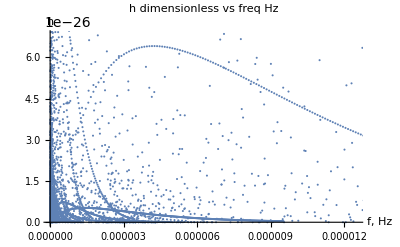

```mathematica
ListPlot[hhVfreq,
PlotLabel->"h dimensionless vs freq Hz",
AxesLabel->{"f, Hz", "h"}]
```

Now do the same with the Amaro-Seoane et al. factor of sqrt(N_obs) to calculate their h_obs, still dimensionless.

```mathematica
hhVfreq={}; (* Hold data for plotting, giant flat list. *)
tobs = 10.*secsYear;

For[ipl=1, ipl≤Length[fdata], ipl++,
{Block[{row, m1,m2, smax, dL},  (* use the Block[] to have some local variables. *)
frow = fdata[[ipl]];
orbeccen = frow[[cols["pl_orbeccen"] ]];
modeMax = Ceiling[ fitEcc2N2[orbeccen] ];(* max harmonic n for eccen *)
If[ipl<2,Print["orbeccen ", orbeccen, " modeMax ", modeMax]]; (* check the above lookup *)
m1 = frow[[cols["pl_bmassj"]] ]*massJ;
m2= frow[[cols["st_mass"]] ]*massSun;
smax = frow[[cols["pl_orbsmax"]] ]*au ;
dL = frow[[cols["st_dist"] ]]*pc;
freq0= 1.0/( frow[[cols["pl_orbper"] ]]*secsDay );
frontCoeff = bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/dL(2π freq0)^(2/3);

(* see above, missing the sqrt(g(n,e))/n in Amaro-Seoane's eqn. *)
],(* end Block *)  
For[imode = 1, imode ≤  modeMax, imode++,
Block[{gwfreq, hh, factAS},
gwfreq = freq0*imode;
factAS = rootNfcn[  1/freq0, tobs, imode]; (* Torb, Tobs, n-mode *)
hh = frontCoeff*Sqrt[ggAS[imode, orbeccen] ]/imode *factAS;
hhVfreq~AppendTo~{gwfreq, hh};
](* end second Block *)
](* end second For loop *)
}(* end {} for first For loop *)
](* end first For *)
```

orbeccen 0.53 modeMax 15

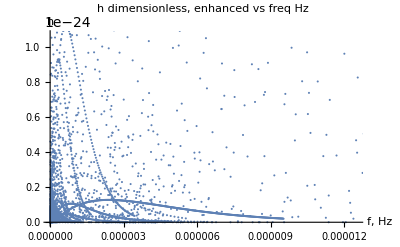

```mathematica
ListPlot[hhVfreq,
PlotLabel->"h dimensionless, enhanced vs freq Hz",
AxesLabel->{"f, Hz", "h"}]
```

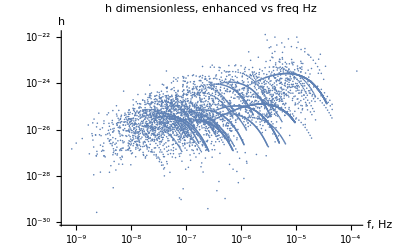

```mathematica
ListLogLogPlot[hhVfreq,
PlotLabel->"h dimensionless, enhanced vs freq Hz",
AxesLabel->{"f, Hz", "h"}]
```